```mathematica
(A = {{0.1049, 0.4568},{1.0000,1.0000},{0.8814,0.7894},{0.6829,0.2003}}) // MatrixForm
J = Inverse[Transpose[A].A].Transpose[A];
```

(0.1049 | 0.4568
1. | 1.
0.8814 | 0.7894
0.6829 | 0.2003)

```mathematica
(x = {1.0, 0.5}) // MatrixForm
```

(1.
0.5)

A represents product ion intensities for PGE2 and PGD2
x represents abundances for PGE2 and PGD2
b represents observed product ion intensities

```mathematica
(* Observed spectrum for test *)
(b = A.x) // MatrixForm
```

(0.3333
1.5
1.2761
0.78305)

```mathematica
(* Solve an equation *)
J.b // MatrixForm
```

(1.
0.5)

```mathematica
σ=Symbol["σ"];
```

```mathematica
SigmaB=σ^2 IdentityMatrix[4];
```

```mathematica
(SigmaX=Simplify[J.SigmaB.Transpose[J]]) // MatrixForm
```

(0.+2.73852 σ^2 | 0.-2.75101 σ^2
0.-2.75101 σ^2 | 0.+3.29777 σ^2)

```mathematica
StandardErrors=Sqrt[Diagonal[SigmaX]]
```

{√(0.+2.73852 σ^2),√(0.+3.29777 σ^2)}

```mathematica
(*Norms of each column*)colNorms=Norm/@Transpose[A]

(*Cosine similarity (dot product divided by norms)*)
cosSim=(A[[All,1]].A[[All,2]])/(Norm[A[[All,1]]]*Norm[A[[All,2]]])

(*Angle between columns in degrees*)
angle=ArcCos[cosSim]*180/Pi

(*Condition number*)
condNumber=ConditionNumber[A]

Grid[{{"Norm of column 1",colNorms[[1]]},{"Norm of column 2",colNorms[[2]]},{"Cosine similarity",cosSim},{"Angle (degrees)",angle},{"Condition number",condNumber}},Frame->All]
```

{1.50141,1.36819}

0.915429

23.7333

ConditionNumber[{{0.1049,0.4568},{1.,1.},{0.8814,0.7894},{0.6829,0.2003}}]

Norm of column 1 | 1.50141
Norm of column 2 | 1.36819
Cosine similarity | 0.915429
Angle (degrees) | 23.7333
Condition number | ConditionNumber[{{0.1049,0.4568},{1.,1.},{0.8814,0.7894},{0.6829,0.2003}}]

```mathematica
AnalyzeOrthogonality[A_]:=Module[{colNorms,cosSim,angle,condNumber},colNorms=Norm/@Transpose[A];
cosSim=(A[[All,1]].A[[All,2]])/(Norm[A[[All,1]]]*Norm[A[[All,2]]]);
angle=ArcCos[cosSim]*180/Pi;
condNumber=ConditionNumber[A];
Print["Numerical Summary:"];
Grid[{{"Norm of column 1",colNorms[[1]]},{"Norm of column 2",colNorms[[2]]},{"Cosine similarity",cosSim},{"Angle (degrees)",angle},{"Condition number",condNumber}},Frame->All];
Print["\nSpectral Plot:"];
ListLinePlot[{A[[All,1]],A[[All,2]]},PlotStyle->{Red,Blue},PlotMarkers->Automatic,PlotLegends->{"PGE2","PGD2"},Frame->True,FrameLabel->{"Channel Index","Normalized Intensity"},PlotLabel->"Spectral Comparison"]]
```

Numerical Summary:

Spectral Plot:

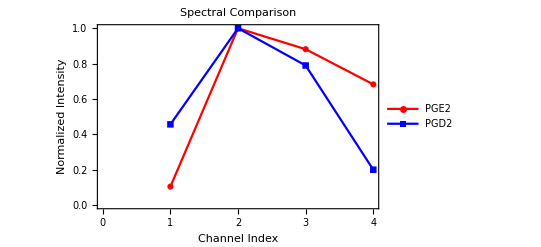

```mathematica
AnalyzeOrthogonality[A]
```

```mathematica
σb=1;
covMatrix=σb^2 Inverse[Transpose[A].A];
rmsErrors=Sqrt@Diagonal[covMatrix]
```

{1.65485,1.81598}

```mathematica
(A2 = {{0.1049, 0.4568},{0.8814,0.7894},{0.6829,0.2003}}) // MatrixForm
```

(0.1049 | 0.4568
0.8814 | 0.7894
0.6829 | 0.2003)

```mathematica
Sqrt@Diagonal[ σb^2 Inverse[Transpose[A2].A2]]
```

{1.65495,1.98485}